#### **********************************************************************************************************************************************************************************************************

#### Hamiltonian (p^2 | Ω1/2 | 0 | Ω2/2 Ω1/2 | p^2 | Ω2/2 | 0 0 | Ω2/2 | -4-4 p+(2+p)^2 | Ω1/2 Ω2/2 | 0 | Ω1/2 | -4-4 p+(2+p)^2)

```mathematica
H[p_,Ω1_,Ω2_]:={{p^2,Ω1/2,0,Ω2/2},{Ω1/2,p^2,Ω2/2,0},{0,Ω2/2,(p+2)^2-4-4p,Ω1/2},{Ω2/2,0,Ω1/2,(p+2)^2-4-4p}}
```

#### Eigenenergy

```mathematica
spectrum=Eigenvalues[H[p,Ω1,Ω2]]//FullSimplify
```

{p^2-Ω1/2-Ω2/2,1/2 (2 p^2+Ω1-Ω2),1/2 (2 p^2-Ω1+Ω2),1/2 (2 p^2+Ω1+Ω2)}

#### Eigenstate

```mathematica
eigenstate=FullSimplify[Table[Normalize[Eigensystem[H[p,Ω1,Ω2]][[2]][[i]]],{i,1,4}],Assumptions->{Ω1∈Reals&&Ω2∈Reals&&Ω1>0&&Ω2>0&&p∈Reals}]
```

{{-1/2,1/2,-1/2,1/2},{-1/2,-1/2,1/2,1/2},{1/2,-1/2,-1/2,1/2},{1/2,1/2,1/2,1/2}}

#### Spectrum

```mathematica
eigen1[p_,Ω1_,Ω2_]=spectrum[[1]];
eigen2[p_,Ω1_,Ω2_]=spectrum[[2]];
eigen3[p_,Ω1_,Ω2_]=spectrum[[3]];
eigen4[p_,Ω1_,Ω2_]=spectrum[[4]];
```

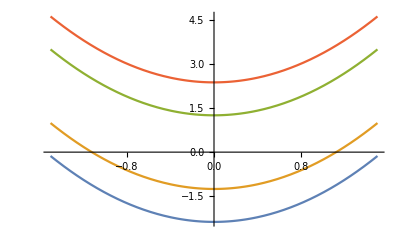

```mathematica
Ω1=1.14/1.014;
Ω2=2*1.845/1.014;
Plot[{eigen1[p,Ω1,Ω2],eigen2[p,Ω1,Ω2],eigen3[p,Ω1,Ω2],eigen4[p,Ω1,Ω2]},{p,-1.5,1.5}]
Clear[Ω1,Ω2]
```

#### initial state (1,0,0,0)^T decomposed into a superposition of the eigenstate of H

```mathematica
stateini={1,0,0,0};
statedresed=FullSimplify[{stateini.Conjugate[eigenstate[[1]]],stateini.Conjugate[eigenstate[[2]]],stateini.Conjugate[eigenstate[[3]]],stateini.Conjugate[eigenstate[[4]]]},Assumptions->{Ω1∈Reals&&Ω2∈Reals&&Ω1>0&&Ω2>0&&p∈Reals}]
```

{-1/2,-1/2,1/2,1/2}

#### Time evolution of the system state starting from the initial state (1,0,0,0)^T

```mathematica
StateDressedTime[t_]={ⅇ^(-ⅈ 2π eigen1[0,Ω1,Ω2] t)statedresed[[1]],ⅇ^(-ⅈ 2π eigen2[0,Ω1,Ω2] t)statedresed[[2]],ⅇ^(-ⅈ 2π eigen3[0,Ω1,Ω2] t)statedresed[[3]],ⅇ^(-ⅈ 2π eigen4[0,Ω1,Ω2] t)statedresed[[4]]}
```

{-1/2 ⅇ^(-2 ⅈ π t (-Ω1/2-Ω2/2)),-1/2 ⅇ^(-ⅈ π t (Ω1-Ω2)),1/2 ⅇ^(-ⅈ π t (-Ω1+Ω2)),1/2 ⅇ^(-ⅈ π t (Ω1+Ω2))}

#### Change to the undressed basis

```mathematica
StateUndressedTime[t_,Ω1_,Ω2_]=StateDressedTime[t][[1]]*eigenstate[[1]]+StateDressedTime[t][[2]]eigenstate[[2]]+StateDressedTime[t][[3]]eigenstate[[3]]+StateDressedTime[t][[4]]eigenstate[[4]]//FullSimplify
```

{Cos[π t Ω1] Cos[π t Ω2],-ⅈ Cos[π t Ω2] Sin[π t Ω1],-Sin[π t Ω1] Sin[π t Ω2],-ⅈ Cos[π t Ω1] Sin[π t Ω2]}

#### Time evolution of the population for state 1, 2 , 3 and 4

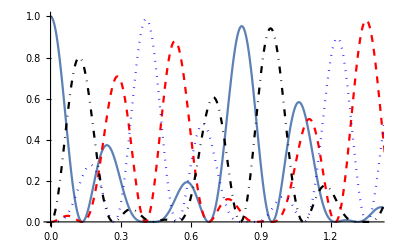

```mathematica
Ω1=1.14/1.014;
Ω2=2*1.845/1.014;
Show[Plot[Abs[StateUndressedTime[t*1.014,Ω1,Ω2][[1]]]^2,{t,0,2}],Plot[Abs[StateUndressedTime[t*1.014,Ω1,Ω2][[2]]]^2,{t,0,2},PlotStyle->{Red,Dashed}],Plot[Abs[StateUndressedTime[t*1.014,Ω1,Ω2][[3]]]^2,{t,0,2},PlotStyle->{Blue,Dotted}],Plot[Abs[StateUndressedTime[t*1.014,Ω1,Ω2][[4]]]^2,{t,0,2},PlotStyle->{Black,DotDashed}],PlotRange->{{0,1.4},All}]
Clear[Ω1,Ω2]
```